```mathematica
DeleteCases[Flatten[Table[{i,j}*Boole[i<j],{i,1,10},{j,1,10}],1],{0,0}]
Table[{%[[i]],i},{i,1,Length[%]}]
```

{{1,2},{1,3},{1,4},{1,5},{1,6},{1,7},{1,8},{1,9},{1,10},{2,3},{2,4},{2,5},{2,6},{2,7},{2,8},{2,9},{2,10},{3,4},{3,5},{3,6},{3,7},{3,8},{3,9},{3,10},{4,5},{4,6},{4,7},{4,8},{4,9},{4,10},{5,6},{5,7},{5,8},{5,9},{5,10},{6,7},{6,8},{6,9},{6,10},{7,8},{7,9},{7,10},{8,9},{8,10},{9,10}}

{{{1,2},1},{{1,3},2},{{1,4},3},{{1,5},4},{{1,6},5},{{1,7},6},{{1,8},7},{{1,9},8},{{1,10},9},{{2,3},10},{{2,4},11},{{2,5},12},{{2,6},13},{{2,7},14},{{2,8},15},{{2,9},16},{{2,10},17},{{3,4},18},{{3,5},19},{{3,6},20},{{3,7},21},{{3,8},22},{{3,9},23},{{3,10},24},{{4,5},25},{{4,6},26},{{4,7},27},{{4,8},28},{{4,9},29},{{4,10},30},{{5,6},31},{{5,7},32},{{5,8},33},{{5,9},34},{{5,10},35},{{6,7},36},{{6,8},37},{{6,9},38},{{6,10},39},{{7,8},40},{{7,9},41},{{7,10},42},{{8,9},43},{{8,10},44},{{9,10},45}}

```mathematica
InterpolatingPolynomial[%,{x,y}]
```

-10+(19/2-x/2) x+y

```mathematica
-10+(19/2-7/2) 7+9
```

41

```mathematica
form[n_]:=Block[{ll=DeleteCases[Flatten[Table[{i,j}*Boole[i<j],{i,1,n},{j,1,n}],1],{0,0}]},
InterpolatingPolynomial[Table[{ll[[i]],i},{i,1,Length[ll]}],{x,y}]]
```

```mathematica
Table[{i,form[i]},{i,3,20}]//Column
```

{3,-2+x+y}
{4,-4+(7/2-x/2) x+y}
{5,-5+(9/2-x/2) x+y}
{6,-6+(11/2-x/2) x+y}
{7,-7+(13/2-x/2) x+y}
{8,-8+(15/2-x/2) x+y}
{9,-9+(17/2-x/2) x+y}
{10,-10+(19/2-x/2) x+y}
{11,-11+(21/2-x/2) x+y}
{12,-12+(23/2-x/2) x+y}
{13,-13+(25/2-x/2) x+y}
{14,-14+(27/2-x/2) x+y}
{15,-15+(29/2-x/2) x+y}
{16,-16+(31/2-x/2) x+y}
{17,-17+(33/2-x/2) x+y}
{18,-18+(35/2-x/2) x+y}
{19,-19+(37/2-x/2) x+y}
{20,-20+(39/2-x/2) x+y}

```mathematica
pair2int[n_,x_,y_]:=-n+((2n-1)/2-x/2)x+y (* n > 2 *)
```

```mathematica
pl[n_]:=DeleteCases[Flatten[Table[{i,j}*Boole[i<j],{i,1,n},{j,1,n}],1],{0,0}]
```

```mathematica
Reduce[-10+(19/2-x/2) x+y==z&&0<z<46&&10≥x>0&&10≥y>0&&x<y,{x,y},Integers]
```

((z==1&&x==1)||(z==2&&x==1)||(z==3&&x==1)||(z==4&&x==1)||(z==5&&x==1)||(z==6&&x==1)||(z==7&&x==1)||(z==8&&x==1)||(z==9&&x==1)||(z==10&&x==2)||(z==11&&x==2)||(z==12&&x==2)||(z==13&&x==2)||(z==14&&x==2)||(z==15&&x==2)||(z==16&&x==2)||(z==17&&x==2)||(z==18&&x==3)||(z==19&&x==3)||(z==20&&x==3)||(z==21&&x==3)||(z==22&&x==3)||(z==23&&x==3)||(z==24&&x==3)||(z==25&&x==4)||(z==26&&x==4)||(z==27&&x==4)||(z==28&&x==4)||(z==29&&x==4)||(z==30&&x==4)||(z==31&&x==5)||(z==32&&x==5)||(z==33&&x==5)||(z==34&&x==5)||(z==35&&x==5)||(z==36&&x==6)||(z==37&&x==6)||(z==38&&x==6)||(z==39&&x==6)||(z==40&&x==7)||(z==41&&x==7)||(z==42&&x==7)||(z==43&&x==8)||(z==44&&x==8)||(z==45&&x==9))&&y==1/2 (20-19 x+x^2+2 z)

```mathematica
"Gives the first position of x as the first element of a pair";
```

```mathematica
firstpos[n_]:=Expand[InterpolatingPolynomial[Table[{i,Min[Flatten[Position[Map[First,pl[n]],i]]]},{i,1,n-1}],x]]
```

```mathematica
pl[10];
Table[{%[[i]],i},{i,1,Length[%]}]
```

{{{1,2},1},{{1,3},2},{{1,4},3},{{1,5},4},{{1,6},5},{{1,7},6},{{1,8},7},{{1,9},8},{{1,10},9},{{2,3},10},{{2,4},11},{{2,5},12},{{2,6},13},{{2,7},14},{{2,8},15},{{2,9},16},{{2,10},17},{{3,4},18},{{3,5},19},{{3,6},20},{{3,7},21},{{3,8},22},{{3,9},23},{{3,10},24},{{4,5},25},{{4,6},26},{{4,7},27},{{4,8},28},{{4,9},29},{{4,10},30},{{5,6},31},{{5,7},32},{{5,8},33},{{5,9},34},{{5,10},35},{{6,7},36},{{6,8},37},{{6,9},38},{{6,10},39},{{7,8},40},{{7,9},41},{{7,10},42},{{8,9},43},{{8,10},44},{{9,10},45}}

```mathematica
Map[({-(firstposition[#[[1]][[1]],11]+1)+#[[2]]+#[[1]][[1]]-#[[1]][[2]]+1})&,Out[81]]
```

{{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0}}

```mathematica
-(firstposition[#[[1]][[1]],11]+1)+#[[2]]+#[[1]][[1]]-#[[1]][[2]]+1
```

```mathematica
-(firstposition[x,n+1]+1)+p+x-y+1
```

```mathematica
Solve[-(f+1)+p+x-y+1==0,y]
```

{{y→-f+p+x}}

```mathematica
HornerForm[p+x-firstposition[x,n+1]]
```

p+n (1-x)+(1/2+x/2) x

```mathematica
fma[fma[x,1/2,1/2],x,fma[1-x,n,p]]
```

p+n (1-x)+(1/2+x/2) x

```mathematica
p+x-firstposition[x,n+1]==y
```

```mathematica
prefinaltest[n_]:=Block[{plist=pl[n]},
Map[(-(firstposition[#[[1]][[1]],n+1]+1)+#[[2]]+#[[1]][[1]]-#[[1]][[2]]+1)&,Table[{plist[[i]],i},{i,1,Length[plist]}]]]
```

```mathematica
Table[prefinaltest[i],{i,4,10}]//Column
```

{0,0,0,0,0,0}
{0,0,0,0,0,0,0,0,0,0}
{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}
{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}
{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}
{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}
{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
firstposition[x_,n_]:=-(n-1)+(2n-1)/2 x-x^2/2 (*for n>3*)
```

```mathematica
Expand[-firstposition[x,n+1]+p+x]
```

n+p+x/2-n x+x^2/2

```mathematica
firstposition[3,11]+1
```

18

```mathematica
Map[(#[[1]][[2]]-#[[1]][[1]])&,Out[81]]
Flatten[Position[%,1]]
Table[{i,%[[i]]},{i,1,Length[%]}]
InterpolatingPolynomial[%,x]
Expand[%]
```

{1,2,3,4,5,6,7,8,9,1,2,3,4,5,6,7,8,1,2,3,4,5,6,7,1,2,3,4,5,6,1,2,3,4,5,1,2,3,4,1,2,3,1,2,1}

{1,10,18,25,31,36,40,43,45}

{{1,1},{2,10},{3,18},{4,25},{5,31},{6,36},{7,40},{8,43},{9,45}}

1+(9+(2-x)/2) (-1+x)

-9+(21 x)/2-x^2/2

```mathematica
Table[{i,Min[Flatten[Position[Map[First,pl[10]],i]]]},{i,1,10-1}]
```

{{1,1},{2,10},{3,18},{4,25},{5,31},{6,36},{7,40},{8,43},{9,45}}

```mathematica
Table[{i,firstpos[i]},{i,4,10}]//Column
```

{4,-3+(9 x)/2-x^2/2}
{5,-4+(11 x)/2-x^2/2}
{6,-5+(13 x)/2-x^2/2}
{7,-6+(15 x)/2-x^2/2}
{8,-7+(17 x)/2-x^2/2}
{9,-8+(19 x)/2-x^2/2}
{10,-9+(21 x)/2-x^2/2}

```mathematica
firstposition[x_,n_]:=-(n-1)+(2n-1)/2 x-x^2/2 (*for n>3*)
```

```mathematica
x/.Solve[-(n-1)+(2n-1)/2 x-x^2/2==p&&p>0&&n>x>0&&n>2,x,Integers]
```

{ConditionalExpression[1/2 (-1+2 n)-1/2 √(9-12 n+4 n^2-8 p),((n|p|x)∈Integers&&p>0&&n≥3&&2-3 n+n^2-2 p≥0)||((n|p|x)∈Integers&&n≥3&&2-3 n+n^2-2 p<0&&9-12 n+4 n^2-8 p>0)],ConditionalExpression[1/2 (-1+2 n)+1/2 √(9-12 n+4 n^2-8 p),(n|p|x)∈Integers&&2-3 n+n^2-2 p<0&&9-12 n+4 n^2-8 p>0&&n≥3]}

```mathematica
pl[10]
Table[{%[[i]],i},{i,1,Length[%]}]
Map[x[#[[2]],10]-#[[1,1]]&,%]
```

{{1,2},{1,3},{1,4},{1,5},{1,6},{1,7},{1,8},{1,9},{1,10},{2,3},{2,4},{2,5},{2,6},{2,7},{2,8},{2,9},{2,10},{3,4},{3,5},{3,6},{3,7},{3,8},{3,9},{3,10},{4,5},{4,6},{4,7},{4,8},{4,9},{4,10},{5,6},{5,7},{5,8},{5,9},{5,10},{6,7},{6,8},{6,9},{6,10},{7,8},{7,9},{7,10},{8,9},{8,10},{9,10}}

{{{1,2},1},{{1,3},2},{{1,4},3},{{1,5},4},{{1,6},5},{{1,7},6},{{1,8},7},{{1,9},8},{{1,10},9},{{2,3},10},{{2,4},11},{{2,5},12},{{2,6},13},{{2,7},14},{{2,8},15},{{2,9},16},{{2,10},17},{{3,4},18},{{3,5},19},{{3,6},20},{{3,7},21},{{3,8},22},{{3,9},23},{{3,10},24},{{4,5},25},{{4,6},26},{{4,7},27},{{4,8},28},{{4,9},29},{{4,10},30},{{5,6},31},{{5,7},32},{{5,8},33},{{5,9},34},{{5,10},35},{{6,7},36},{{6,8},37},{{6,9},38},{{6,10},39},{{7,8},40},{{7,9},41},{{7,10},42},{{8,9},43},{{8,10},44},{{9,10},45}}

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
x[p_,n_]:=Max[Flatten[Position[Map[Boole[p≥#]&,Table[firstposition[i,n+1]+1,{i,1,n-1}]],1]]]
```

```mathematica
HornerForm[firstposition[p,n+1]+1]
```

```mathematica
px[p_,n_]:=1+n (-1+p)+(1/2-p/2) p
```

```mathematica
px[5,10]
```

31

```mathematica
fma[x,y,z]=x y+z
```

x y+z

```mathematica
1+n *(p-1)+(1/2-p/2) p
```

```mathematica
a==1/2-p/2->fma[p,-0.5, 1/2]
1+n *(p-1)+a p
fma[fma[p,-0.5, 1/2], p, fma[n,p-1,1]]
```

```mathematica
fma[x_,y_,z_]:=(x*y)+z
```

```mathematica
fma[fma[p,-0.5, 1/2], p, fma[n,p-1,1]]
```

1+n (-1+p)+(1/2-0.5 p) p

```mathematica
fma[5,-1/2,1/2]
```

-2

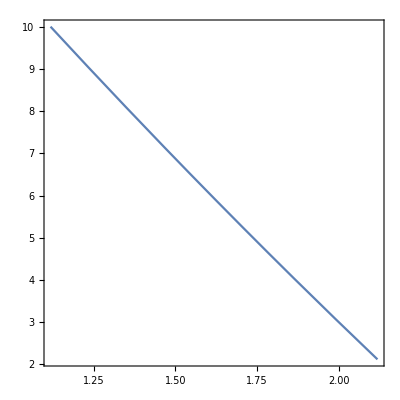

```mathematica
RegionPlot[ImplicitRegion[(0<x<1/2 (21-√281)||x>1/2 (21+√281))&&y==1/2 (40-19 x+x^2),{x,y}]]
```

```mathematica
Expand[-10+(19/2-x/2) x+y==10]
```

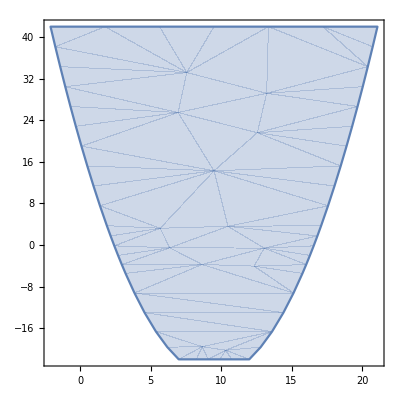

```mathematica
RegionPlot[ImplicitRegion[-10+(19 x)/2-x^2/2+y>10,{x,y}]]
```

```mathematica
pair2int[mm,xvar[i,mm], yvar[i,mm]]
```

0.+i

```mathematica
numofpairs[maxval_]:=fma[maxval,0.5,-0.5]*maxval
```

```mathematica
np2[mm_]:=Sum[Boole[i<j],{i,1,mm},{j,1,mm}]
```

```mathematica
Sum[Boole[np2[i]==numofpairs[i]],{i,1,500}]
```

500

```mathematica
xvarpoly[x_,n_]:=fma[fma[x,-0.5,0.5],x,fma[n,x-1,1]]
xvar[p_,n_]:=Block[{x0=1},While[xvarpoly[x0,n]<p+2, x0++];  x0-1]
yvar[p_,n_]:=Block[{x0=xvar[p,n]},fma[fma[x0,0.5,0.5],x0,fma[1-x0,n,p]]]+1
pair2int[n_,x_,y_]:=fma[fma[x,-0.5,-0.5],x,fma[x-1,n,y]]-1
Table[{{xvar[i,10],yvar[i,10]},i==pair2int[10,xvar[i,10], yvar[i,10]]},{i,0,44}]//Column
```

{{1,2.},True}
{{1,3.},True}
{{1,4.},True}
{{1,5.},True}
{{1,6.},True}
{{1,7.},True}
{{1,8.},True}
{{1,9.},True}
{{1,10.},True}
{{2,3.},True}
{{2,4.},True}
{{2,5.},True}
{{2,6.},True}
{{2,7.},True}
{{2,8.},True}
{{2,9.},True}
{{2,10.},True}
{{3,4.},True}
{{3,5.},True}
{{3,6.},True}
{{3,7.},True}
{{3,8.},True}
{{3,9.},True}
{{3,10.},True}
{{4,5.},True}
{{4,6.},True}
{{4,7.},True}
{{4,8.},True}
{{4,9.},True}
{{4,10.},True}
{{5,6.},True}
{{5,7.},True}
{{5,8.},True}
{{5,9.},True}
{{5,10.},True}
{{6,7.},True}
{{6,8.},True}
{{6,9.},True}
{{6,10.},True}
{{7,8.},True}
{{7,9.},True}
{{7,10.},True}
{{8,9.},True}
{{8,10.},True}
{{9,10.},True}

{0,11.}
{1,3.}
{1,4.}
{1,5.}
{1,6.}
{1,7.}
{1,8.}
{1,9.}
{1,10.}
{1,11.}
{2,4.}
{2,5.}
{2,6.}
{2,7.}
{2,8.}
{2,9.}
{2,10.}
{2,11.}
{3,5.}
{3,6.}
{3,7.}
{3,8.}
{3,9.}
{3,10.}
{3,11.}
{4,6.}
{4,7.}
{4,8.}
{4,9.}
{4,10.}
{4,11.}
{5,7.}
{5,8.}
{5,9.}
{5,10.}
{5,11.}
{6,8.}
{6,9.}
{6,10.}
{6,11.}
{7,9.}
{7,10.}
{7,11.}
{8,10.}
{8,11.}

```mathematica
fma[x_,y_,z_]:=x y+z
```